

```mathematica
Graphics[Disk[]]
```

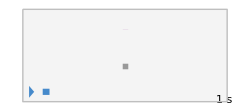

```mathematica
Sound[SoundNote["C"]]
```

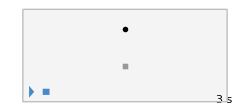

```mathematica
Sound[{SoundNote["C"],SoundNote["C"],SoundNote["E"]}]
```

```mathematica
Sound[{SoundNote[0],SoundNote[0], SoundNote[4]}]
```

-Graphics-

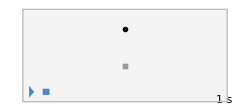

```mathematica
Sound[{SoundNote[0,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[5,0.2], SoundNote[7,0.2]}]
```

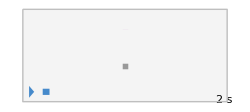

```mathematica
Sound[SoundNote[0,2,"Violin"]]
```

```mathematica
Sound[{SoundNote[0,{0,3},"Violin"],SoundNote[5{1,3},"Violin"],SoundNote[9,{2,3},"Violin"]}]
```

Sound[{SoundNote[0,{0,3},Violin],SoundNote[{5,15},Violin],SoundNote[9,{2,3},Violin]}]

```mathematica
Table[SoundNote[n,0.2],{n,5}]
```

{SoundNote[1,0.2],SoundNote[2,0.2],SoundNote[3,0.2],SoundNote[4,0.2],SoundNote[5,0.2]}

```mathematica
Sound[Table[SoundNote[n,0.2],{n,5}]]
```

-Graphics-

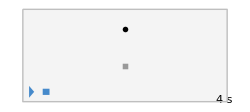

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Violin"],20]]
```

```mathematica
EmitSound[Sound[Table[SoundNote[RandomInteger[12],0.2,"Violin"],20]]]
```

```mathematica
Table[f[n],{n,{2,5,8,1,7}}]
```

{f[2],f[5],f[8],f[1],f[7]}

```mathematica
{0,0,7,7,9,9,7,4,5,2,4,0,2,-1,0}
```

{0,0,7,7,9,9,7,4,5,2,4,0,2,-1,0}

```mathematica
Sound[Table[SoundNote[n,0.2,"Violin"],{n,{0,0,7,7,9,9,7,4,5,2,4,0,2,-1,0}}]]
```

-Graphics-

```mathematica
{4,4,4,4,4,4,4,4,4,4,7,4,7,4,7,4,7,4,7,4,7,4,4,5,6,7,5,6,4,2}
```

{4,4,4,4,4,4,4,4,4,4,7,4,7,4,7,4,7,4,7,4,7,4,4,5,6,7,5,6,4,2}

```mathematica
Sound[Table[SoundNote[n,0.15,"violin"],{n,{4,4,4,4,4,4,4,4,4,4,7,4,7,4,7,4,7,4,7,4,7,4,4,5,6,7,5,6,4,2}}]]
```

Sound[{SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[7,0.15,violin],SoundNote[4,0.15,violin],SoundNote[7,0.15,violin],SoundNote[4,0.15,violin],SoundNote[7,0.15,violin],SoundNote[4,0.15,violin],SoundNote[7,0.15,violin],SoundNote[4,0.15,violin],SoundNote[7,0.15,violin],SoundNote[4,0.15,violin],SoundNote[7,0.15,violin],SoundNote[4,0.15,violin],SoundNote[4,0.15,violin],SoundNote[5,0.15,violin],SoundNote[6,0.15,violin],SoundNote[7,0.15,violin],SoundNote[5,0.15,violin],SoundNote[6,0.15,violin],SoundNote[4,0.15,violin],SoundNote[2,0.15,violin]}]

vacabulary
	Sound[(...)]
    	SoundNote["C"]
        	SoundNote[5]
            	SoundNote[5,0.1]
               SoundNote[5,{1,3}]
               SoundNote[5,1,"Violin"]

```mathematica
-------------------------------------------------------
```

```mathematica
Characters["CABBAGE"]
```

{C,A,B,B,A,G,E}

```mathematica
Table[SoundNote[n,0.3, "Guitar"], {n,Characters["CABBAGE"]}]
```

{SoundNote[C,0.3,Guitar],SoundNote[A,0.3,Guitar],SoundNote[B,0.3,Guitar],SoundNote[B,0.3,Guitar],SoundNote[A,0.3,Guitar],SoundNote[G,0.3,Guitar],SoundNote[E,0.3,Guitar]}

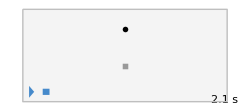

```mathematica
Sound[Table[SoundNote[n,0.3, "Guitar"], {n,Characters["CABBAGE"]}]]
```